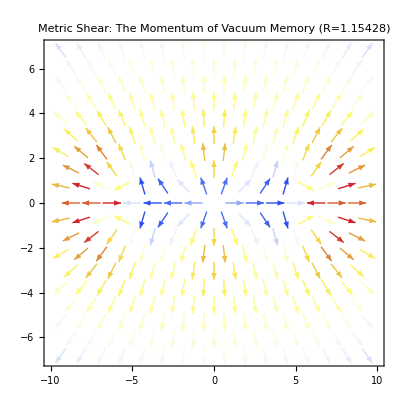

```mathematica
(*The Vanguard Audit:Metric Shear Vector Field*)ClearAll["Global`*"];
R=1.15428;
offVal=6.0;
softening=0.1;

(*Gradient of the Lensing Potential represents the Shear Flow*)
Potential[x_,y_]:=(1.0/Sqrt[x^2+y^2+softening]+(R*Log[Sqrt[x^2+y^2+softening]]))+(1.2/Sqrt[(x-offVal)^2+y^2+softening]+(R*Log[Sqrt[(x-offVal)^2+y^2+softening]]))+(1.2/Sqrt[(x+offVal)^2+y^2+softening]+(R*Log[Sqrt[(x+offVal)^2+y^2+softening]]));

VectorPlot[Evaluate[Grad[Potential[x,y],{x,y}]],{x,-10,10},{y,-7,7},VectorStyle->"Arrowhead",VectorColorFunction->"TemperatureMap",PlotLabel->"Metric Shear: The Momentum of Vacuum Memory (R=1.15428)"]
```